# VertexCloseness

Calculates the average distance of a vertex to all other vertices it is connected to in the graph

## Definition

```mathematica
ClearAll[VertexCloseness]
VertexCloseness[g_?GraphQ,v_]:=N@Length[DeleteCases[GraphDistance[g,v],0]]/Total[GraphDistance[g,v]]/;MemberQ[VertexList[g],v]
```

## Documentation

### Usage

VertexCloseness[graph, vertex]

finds the average distance from the vertex in graph to the other vertexes the vertex is connected to.

### Details & Options

ClosenessCentrality[g] is equivalent to VertexCloseness[g,#]&/@VertexList[g]]

## Examples

### Basic Examples

Make a Manipulate of the vertex closeness of example data friendship network:

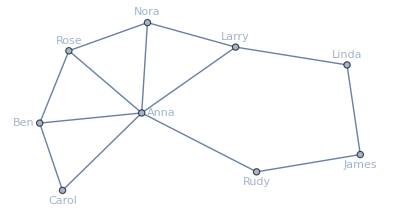

```mathematica
g=ExampleData[{"NetworkGraph","Friendship"}]
```

```mathematica
Manipulate[HighlightGraph[g,VertexList[g],VertexSize-> Thread[VertexList[g]-> Rescale[ClosenessCentrality[g]]],VertexLabels->{v->Placed[StringJoin[v," has a vertex closeness of ",ToString@VertexCloseness[g,v]],Tooltip]}],{v,VertexList[g]},SaveDefinitions->True]
```

-Graphics-

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph Centrality Measures

Graph Theory

Social Network Analysis

Graph Measures and Metrics

Graph Properties and Measurement

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related Symbols

ClosenessCentrality

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.